```mathematica
ClearAll["Global`*"]
```

Define colors for graphs

```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
```

## Master equation of a optically controlled quantum thermal gate in the full 8×8 space

The index S represents which transistor is considered.

Eigenstates,
|1> =|+z,+z,+z>
|2> =|+z,+z,-z>
|3> =|+z,-z,+z>
|4> =|+z,-z,-z>
|5> =|-z,+z,+z>
|6> =|-z,+z,-z>
|7> =|-z,-z,+z>
|8> =|-z,-z,-z>

### Density matrix

```mathematica
Subscript[ρMatrix, S_][t_]:=Table[Subscript[ρ, S,i,j][t],{i,1,8},{j,1,8}];
MatrixForm[Subscript[ρMatrix, S][t]]
```

(ρ_(S,1,1)[t] | ρ_(S,1,2)[t] | ρ_(S,1,3)[t] | ρ_(S,1,4)[t] | ρ_(S,1,5)[t] | ρ_(S,1,6)[t] | ρ_(S,1,7)[t] | ρ_(S,1,8)[t]
ρ_(S,2,1)[t] | ρ_(S,2,2)[t] | ρ_(S,2,3)[t] | ρ_(S,2,4)[t] | ρ_(S,2,5)[t] | ρ_(S,2,6)[t] | ρ_(S,2,7)[t] | ρ_(S,2,8)[t]
ρ_(S,3,1)[t] | ρ_(S,3,2)[t] | ρ_(S,3,3)[t] | ρ_(S,3,4)[t] | ρ_(S,3,5)[t] | ρ_(S,3,6)[t] | ρ_(S,3,7)[t] | ρ_(S,3,8)[t]
ρ_(S,4,1)[t] | ρ_(S,4,2)[t] | ρ_(S,4,3)[t] | ρ_(S,4,4)[t] | ρ_(S,4,5)[t] | ρ_(S,4,6)[t] | ρ_(S,4,7)[t] | ρ_(S,4,8)[t]
ρ_(S,5,1)[t] | ρ_(S,5,2)[t] | ρ_(S,5,3)[t] | ρ_(S,5,4)[t] | ρ_(S,5,5)[t] | ρ_(S,5,6)[t] | ρ_(S,5,7)[t] | ρ_(S,5,8)[t]
ρ_(S,6,1)[t] | ρ_(S,6,2)[t] | ρ_(S,6,3)[t] | ρ_(S,6,4)[t] | ρ_(S,6,5)[t] | ρ_(S,6,6)[t] | ρ_(S,6,7)[t] | ρ_(S,6,8)[t]
ρ_(S,7,1)[t] | ρ_(S,7,2)[t] | ρ_(S,7,3)[t] | ρ_(S,7,4)[t] | ρ_(S,7,5)[t] | ρ_(S,7,6)[t] | ρ_(S,7,7)[t] | ρ_(S,7,8)[t]
ρ_(S,8,1)[t] | ρ_(S,8,2)[t] | ρ_(S,8,3)[t] | ρ_(S,8,4)[t] | ρ_(S,8,5)[t] | ρ_(S,8,6)[t] | ρ_(S,8,7)[t] | ρ_(S,8,8)[t])

### System Hamiltonian

```mathematica
Subscript[HsMatrix, S_]:=({{1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]+Subscript[ωM, S]+Subscript[ωMR, S]+Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0, 0, 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]+Subscript[ωM, S]-Subscript[ωMR, S]-Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0, 0, 0, 0, 0}, {0, 0, 1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]-Subscript[ωM, S]-Subscript[ωMR, S]+Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0, 0, 0}, {0, 0, 0, 1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]-Subscript[ωM, S]+Subscript[ωMR, S]-Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0, 0, 0}, {0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]-Subscript[ωM, S]-Subscript[ωMR, S]-Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0}, {0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]-Subscript[ωM, S]+Subscript[ωMR, S]+Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0}, {0, 0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]+Subscript[ωM, S]+Subscript[ωMR, S]-Subscript[ωR, S]+Subscript[ωRL, S]), 0}, {0, 0, 0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]+Subscript[ωM, S]-Subscript[ωMR, S]+Subscript[ωR, S]-Subscript[ωRL, S])}})
```

```mathematica
Subscript[HsEVal, S_][i_]:=(Eigenvalues[Subscript[HsMatrix, S]][[{8,1,7,2,4,5,3,6}]])[[i]]
Subscript[HsEVec, S_][i_]:=(Eigenvectors[Subscript[HsMatrix, S]][[{8,1,7,2,4,5,3,6}]])[[i]]
```

Relation between eigenvalues and ωs

```mathematica
ωassum=Flatten[{Table[Subscript[ω, S_,i,j]->(Subscript[HsEVal, S][i]-Subscript[HsEVal, S][j] )/ℏ,{i,1,8},{j,1,8}]}];
```

### Interaction Hamiltonian with the classically modelled optical field

Ω_P represents the strength of the interaction between the device P and the optical field

```mathematica
Subscript[HlMatrix, S_]:= ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

Net optical field induced decaying rate Υ_P[i,j] of the device P from state | i > to state | j > while absorbing energy from the external electric field.
Υs[i,j] is used due to variable naming issues.

```mathematica
Subscript[Υs, S_][i_,j_]:= Subscript[Ω, S]/2 ⅈ(Subscript[ρ, S,i,j][t]-Subscript[ρ, S,j,i][t])
```

### Lindblad operators from environment interactions

Taking results from the previous work (“Optically Controlled Quantum Thermal Gate”). The second variable lists all possible energy transitions and the first lists the corresponding Lindblad operators.

```mathematica
linOps=({{({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})}, {({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})}, {({{0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}})}});
tranfreqs={-ωMR-ωR-ωRL,-ωLM-ωM-ωMR,-ωLM-ωM+ωR+ωRL,-ωLM-ωM-ωR-ωRL,-ωLM-ωM+ωMR,ωMR-ωR-ωRL,-ωL-ωLM-ωRL,-ωL-ωLM+ωMR+ωR,-ωL+ωM+ωMR-ωRL,-ωL+ωM+ωR,-ωL-ωLM-ωMR-ωR,-ωL-ωLM+ωRL,-ωL+ωM-ωR,-ωL+ωM-ωMR+ωRL,-ωMR-ωR+ωRL,-ωL-ωM-ωMR-ωRL,-ωL-ωM+ωR,-ωL+ωLM-ωRL,-ωL+ωLM-ωMR+ωR,ωLM-ωM-ωMR,ωLM-ωM+ωR-ωRL,-ωL-ωM-ωR,-ωL-ωM+ωMR+ωRL,-ωL+ωLM+ωMR-ωR,-ωL+ωLM+ωRL,ωLM-ωM-ωR+ωRL,ωLM-ωM+ωMR,ωMR-ωR+ωRL};
tranfreqssymb={Subscript[ω, {2,1}],Subscript[ω, {3,1}],Subscript[ω, {3,2}],Subscript[ω, {4,1}],Subscript[ω, {4,2}],Subscript[ω, {4,3}],Subscript[ω, {5,1}],Subscript[ω, {5,2}],Subscript[ω, {5,3}],Subscript[ω, {5,4}],Subscript[ω, {6,1}],Subscript[ω, {6,2}],Subscript[ω, {6,3}],Subscript[ω, {6,4}],Subscript[ω, {6,5}],Subscript[ω, {7,1}],Subscript[ω, {7,2}],Subscript[ω, {7,3}],Subscript[ω, {7,4}],Subscript[ω, {7,5}],Subscript[ω, {7,6}],Subscript[ω, {8,1}],Subscript[ω, {8,2}],Subscript[ω, {8,3}],Subscript[ω, {8,4}],Subscript[ω, {8,5}],Subscript[ω, {8,6}],Subscript[ω, {8,7}]}/.Subscript[ω, {i_,j_}]-> Subscript[ω, i,j];
```

We now remove the zero Lindblad operators and extract only the important transitions and their corresponding Lindblad operators.

```mathematica
Subscript[AMatrix, P_][i_]:=Module[{temp1},
temp1=Position[linOps[[P,;;]],Table[0,{j,1,8},{k,1,8}]];
Delete[linOps[[P,;;]],temp1][[i]]
]
Subscript[ω, P_][i_]:=Module[{temp1},
temp1=Position[linOps[[P,;;]],Table[0,{j,1,8},{k,1,8}]];
Delete[tranfreqssymb,temp1][[i]]
]
```

```mathematica
Table[MatrixForm[Subscript[AMatrix, P][i]],{P,1,3},{i,1,4}]//MatrixForm
Table[MatrixForm[Subscript[ω, P][i]],{P,1,3},{i,1,4}]//MatrixForm
```

((0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))

(ω_(5,1) | ω_(6,2) | ω_(7,3) | ω_(8,4)
ω_(3,1) | ω_(4,2) | ω_(7,5) | ω_(8,6)
ω_(2,1) | ω_(4,3) | ω_(6,5) | ω_(8,7))

Insert a “transistor number” variable S,

```mathematica
Subscript[AMatrix, S_,P_][i_]:=Subscript[AMatrix, P][i]
Subscript[ω, S_,P_][i_]:=Subscript[ω, P][i]/.Subscript[ω, j_,k_]->Subscript[ω, S,j,k]
```

The dissipation terms can now be written

```mathematica
Subscript[LinMatrix, S_,P_][ρ_]:=∑_(i=1)^4 (Subscript[J, S,P][Subscript[ω, S,P][i]](1+Subscript[NBE, S,P][Subscript[ω, S,P][i]])(Subscript[AMatrix, S,P][i].ρ.Subscript[AMatrix, S,P][i]†-1/2(Subscript[AMatrix, S,P][i]†.Subscript[AMatrix, S,P][i].ρ+ρ.Subscript[AMatrix, S,P][i]†.Subscript[AMatrix, S,P][i]))+Subscript[J, S,P][Subscript[ω, S,P][i]]Subscript[NBE, S,P][Subscript[ω, S,P][i]](Subscript[AMatrix, S,P][i]†.ρ.Subscript[AMatrix, S,P][i]-1/2(Subscript[AMatrix, S,P][i].Subscript[AMatrix, S,P][i]†.ρ+ρ.Subscript[AMatrix, S,P][i].Subscript[AMatrix, S,P][i]†)))
```

```mathematica
{Subscript[LinMatrix, S,1][Subscript[ρMatrix, S][t]]//MatrixForm,
Subscript[LinMatrix, S,2][Subscript[ρMatrix, S][t]]//MatrixForm,
Subscript[LinMatrix, S,3][Subscript[ρMatrix, S][t]]//MatrixForm}
```

{(1),(1),(1)}
 |  |  |  |

Net thermal decaying rate Τ_(S,P)[i,j] of component S from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_(S,P)[i,j] is used due to variable naming issues.

```mathematica
Subscript[Τs, S_,P_][i_,j_]:=Subscript[J, S,P][Subscript[ω, S,i,j]]((1+Subscript[NBE, S,P][Subscript[ω, S,i,j]])Subscript[ρ, S,i,i][t]-Subscript[NBE, S,P][Subscript[ω, S,i,j]]Subscript[ρ, S,j,j][t])
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, S,1][Subscript[ρMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, S,2][Subscript[ρMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, S,3][Subscript[ρMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]
```

(Τ_(S,1)[5,1] | 1/2 (-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,2)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,3)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,4)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,1,4)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,1,5)[t]-2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,5)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,1,6)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,6)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,1,6)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,1,7)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,7)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,1,7)[t]) | 1/2 (-J_(S,1)[ω_(S,8,4)] ρ_(S,1,8)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,8)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,1,8)[t])
1/2 (-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,2,1)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,1)[t]) | Τ_(S,1)[6,2] | 1/2 (-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,3)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,4)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,2,4)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,2,5)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,2,5)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,5)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,2,6)[t]-2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,6)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,2,7)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,7)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,2,7)[t]) | 1/2 (-J_(S,1)[ω_(S,8,4)] ρ_(S,2,8)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,8)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,2,8)[t])
1/2 (-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,3,1)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,3,2)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,2)[t]) | Τ_(S,1)[7,3] | 1/2 (-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,4)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,3,4)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,3,5)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,3,5)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,5)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,3,6)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,3,6)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,6)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,3,7)[t]-2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,7)[t]) | 1/2 (-J_(S,1)[ω_(S,8,4)] ρ_(S,3,8)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,8)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,3,8)[t])
1/2 (-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,4,1)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,4,2)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,4,3)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,3)[t]) | Τ_(S,1)[8,4] | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,4,5)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,4,5)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,5)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,4,6)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,4,6)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,6)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,4,7)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,4,7)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,7)[t]) | 1/2 (-J_(S,1)[ω_(S,8,4)] ρ_(S,4,8)[t]-2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,8)[t])
1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,5,1)[t]-2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,1)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,5,2)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,2)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,5,2)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,5,3)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,3)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,5,3)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,5,4)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,4)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,5,4)[t]) | -Τ_(S,1)[5,1] | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,5,6)[t]-J_(S,1)[ω_(S,6,2)] ρ_(S,5,6)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,6)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,5,6)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,5,7)[t]-J_(S,1)[ω_(S,7,3)] ρ_(S,5,7)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,7)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,5,7)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,5,8)[t]-J_(S,1)[ω_(S,8,4)] ρ_(S,5,8)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,8)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,5,8)[t])
1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,6,1)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,6,1)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,1)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,6,2)[t]-2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,2)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,6,3)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,3)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,6,3)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,6,4)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,4)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,6,4)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,6,5)[t]-J_(S,1)[ω_(S,6,2)] ρ_(S,6,5)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,6,5)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,5)[t]) | -Τ_(S,1)[6,2] | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,6,7)[t]-J_(S,1)[ω_(S,7,3)] ρ_(S,6,7)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,7)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,6,7)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,6,8)[t]-J_(S,1)[ω_(S,8,4)] ρ_(S,6,8)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,8)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,6,8)[t])
1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,7,1)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,7,1)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,1)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,7,2)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,7,2)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,2)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,7,3)[t]-2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,3)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,7,4)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,4)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,7,4)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,7,5)[t]-J_(S,1)[ω_(S,7,3)] ρ_(S,7,5)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,7,5)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,5)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,7,6)[t]-J_(S,1)[ω_(S,7,3)] ρ_(S,7,6)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,7,6)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,6)[t]) | -Τ_(S,1)[7,3] | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,7,8)[t]-J_(S,1)[ω_(S,8,4)] ρ_(S,7,8)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,8)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,7,8)[t])
1/2 (-J_(S,1)[ω_(S,8,4)] ρ_(S,8,1)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,8,1)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,1)[t]) | 1/2 (-J_(S,1)[ω_(S,8,4)] ρ_(S,8,2)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,8,2)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,2)[t]) | 1/2 (-J_(S,1)[ω_(S,8,4)] ρ_(S,8,3)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,8,3)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,3)[t]) | 1/2 (-J_(S,1)[ω_(S,8,4)] ρ_(S,8,4)[t]-2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,4)[t]) | 1/2 (-J_(S,1)[ω_(S,5,1)] ρ_(S,8,5)[t]-J_(S,1)[ω_(S,8,4)] ρ_(S,8,5)[t]-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,8,5)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,5)[t]) | 1/2 (-J_(S,1)[ω_(S,6,2)] ρ_(S,8,6)[t]-J_(S,1)[ω_(S,8,4)] ρ_(S,8,6)[t]-J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,8,6)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,6)[t]) | 1/2 (-J_(S,1)[ω_(S,7,3)] ρ_(S,8,7)[t]-J_(S,1)[ω_(S,8,4)] ρ_(S,8,7)[t]-J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,8,7)[t]-J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,7)[t]) | -Τ_(S,1)[8,4])

(Τ_(S,2)[3,1] | 1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]-2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,1,4)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,4)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,5)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,1,5)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,6)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,1,6)[t]) | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,1,7)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,7)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,1,7)[t]) | 1/2 (-J_(S,2)[ω_(S,8,6)] ρ_(S,1,8)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,8)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,1,8)[t])
1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,1)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,1)[t]) | Τ_(S,2)[4,2] | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,2,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,3)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t]-2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,5)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,2,5)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,6)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,2,6)[t]) | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,2,7)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,7)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,2,7)[t]) | 1/2 (-J_(S,2)[ω_(S,8,6)] ρ_(S,2,8)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,8)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,2,8)[t])
1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]-2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,2)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,2)[t]) | -Τ_(S,2)[3,1] | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,4,2)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,4)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,5)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,5)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,3,5)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,6)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,6)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,3,6)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,7)[t]-J_(S,2)[ω_(S,7,5)] ρ_(S,3,7)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,7)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,3,7)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,8)[t]-J_(S,2)[ω_(S,8,6)] ρ_(S,3,8)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,8)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,3,8)[t])
1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,1)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,1)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]-2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,4,2)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,3)[t]) | -Τ_(S,2)[4,2] | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,5)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,5)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,4,5)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,6)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,6)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,4,6)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,7)[t]-J_(S,2)[ω_(S,7,5)] ρ_(S,4,7)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,7)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,4,7)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,8)[t]-J_(S,2)[ω_(S,8,6)] ρ_(S,4,8)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,8)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,4,8)[t])
1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,5,1)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,1)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,5,2)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,5,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,5,3)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,5,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,5,4)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,4)[t]) | Τ_(S,2)[7,5] | 1/2 (-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,6)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,5,6)[t]) | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,5,7)[t]-2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,7)[t]) | 1/2 (-J_(S,2)[ω_(S,8,6)] ρ_(S,5,8)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,8)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,5,8)[t])
1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,6,1)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,1)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,6,2)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,6,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,6,3)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,6,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,6,4)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,4)[t]) | 1/2 (-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,6,5)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,5)[t]) | Τ_(S,2)[8,6] | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,6,7)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,6,7)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,7)[t]) | 1/2 (-J_(S,2)[ω_(S,8,6)] ρ_(S,6,8)[t]-2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,8)[t])
1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,7,1)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,7,1)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,1)[t]) | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,7,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,7,2)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,7,3)[t]-J_(S,2)[ω_(S,7,5)] ρ_(S,7,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,7,3)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,7,4)[t]-J_(S,2)[ω_(S,7,5)] ρ_(S,7,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,7,4)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,4)[t]) | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,7,5)[t]-2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,5)[t]) | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,7,6)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,6)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,7,6)[t]) | -Τ_(S,2)[7,5] | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,7,8)[t]-J_(S,2)[ω_(S,8,6)] ρ_(S,7,8)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,8)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,7,8)[t])
1/2 (-J_(S,2)[ω_(S,8,6)] ρ_(S,8,1)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,8,1)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,1)[t]) | 1/2 (-J_(S,2)[ω_(S,8,6)] ρ_(S,8,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,8,2)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,8,3)[t]-J_(S,2)[ω_(S,8,6)] ρ_(S,8,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,8,3)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,8,4)[t]-J_(S,2)[ω_(S,8,6)] ρ_(S,8,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,8,4)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,4)[t]) | 1/2 (-J_(S,2)[ω_(S,8,6)] ρ_(S,8,5)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,8,5)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,5)[t]) | 1/2 (-J_(S,2)[ω_(S,8,6)] ρ_(S,8,6)[t]-2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,6)[t]) | 1/2 (-J_(S,2)[ω_(S,7,5)] ρ_(S,8,7)[t]-J_(S,2)[ω_(S,8,6)] ρ_(S,8,7)[t]-J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,8,7)[t]-J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,7)[t]) | -Τ_(S,2)[8,6])

(Τ_(S,3)[2,1] | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]-2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,1,4)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,4)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,5)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,1,5)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,1,6)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,6)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,1,6)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,7)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,1,7)[t]) | 1/2 (-J_(S,3)[ω_(S,8,7)] ρ_(S,1,8)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,8)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,1,8)[t])
1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]-2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]) | -Τ_(S,3)[2,1] | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,3)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,4,3)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,4)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,5)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,5)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,2,5)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,6)[t]-J_(S,3)[ω_(S,6,5)] ρ_(S,2,6)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,6)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,2,6)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,7)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,7)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,2,7)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,8)[t]-J_(S,3)[ω_(S,8,7)] ρ_(S,2,8)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,8)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,2,8)[t])
1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,1)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,3,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,2)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,2)[t]) | Τ_(S,3)[4,3] | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t]-2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,5)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,3,5)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,3,6)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,6)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,3,6)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,7)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,3,7)[t]) | 1/2 (-J_(S,3)[ω_(S,8,7)] ρ_(S,3,8)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,8)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,3,8)[t])
1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,1)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,1)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,4,3)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]-2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]) | -Τ_(S,3)[4,3] | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,5)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,5)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,4,5)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,6)[t]-J_(S,3)[ω_(S,6,5)] ρ_(S,4,6)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,6)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,4,6)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,7)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,7)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,4,7)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,8)[t]-J_(S,3)[ω_(S,8,7)] ρ_(S,4,8)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,8)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,4,8)[t])
1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,5,1)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,5,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,5,2)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,2)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,5,3)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,3)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,5,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,5,4)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,4)[t]) | Τ_(S,3)[6,5] | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,5,6)[t]-2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,6)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,7)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,5,7)[t]) | 1/2 (-J_(S,3)[ω_(S,8,7)] ρ_(S,5,8)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,8)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,5,8)[t])
1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,6,1)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,6,1)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,6,2)[t]-J_(S,3)[ω_(S,6,5)] ρ_(S,6,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,6,2)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,2)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,6,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,6,3)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,3)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,6,4)[t]-J_(S,3)[ω_(S,6,5)] ρ_(S,6,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,6,4)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,4)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,6,5)[t]-2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,5)[t]) | -Τ_(S,3)[6,5] | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,6,7)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,7)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,6,7)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,6,8)[t]-J_(S,3)[ω_(S,8,7)] ρ_(S,6,8)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,8)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,6,8)[t])
1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,7,1)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,7,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,7,2)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,2)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,7,3)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,3)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,7,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,7,4)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,4)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,7,5)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,5)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,7,6)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,7,6)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,6)[t]) | Τ_(S,3)[8,7] | 1/2 (-J_(S,3)[ω_(S,8,7)] ρ_(S,7,8)[t]-2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,8)[t])
1/2 (-J_(S,3)[ω_(S,8,7)] ρ_(S,8,1)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,8,1)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,8,2)[t]-J_(S,3)[ω_(S,8,7)] ρ_(S,8,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,8,2)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,2)[t]) | 1/2 (-J_(S,3)[ω_(S,8,7)] ρ_(S,8,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,8,3)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,3)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,8,4)[t]-J_(S,3)[ω_(S,8,7)] ρ_(S,8,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,8,4)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,4)[t]) | 1/2 (-J_(S,3)[ω_(S,8,7)] ρ_(S,8,5)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,8,5)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,5)[t]) | 1/2 (-J_(S,3)[ω_(S,6,5)] ρ_(S,8,6)[t]-J_(S,3)[ω_(S,8,7)] ρ_(S,8,6)[t]-J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,8,6)[t]-J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,6)[t]) | 1/2 (-J_(S,3)[ω_(S,8,7)] ρ_(S,8,7)[t]-2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,7)[t]) | -Τ_(S,3)[8,7])

### Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, S_,P_][ω_]->Subscript[κ, S,P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
Subscript[RHSfield, S_]:=-ⅈ/ℏ(Subscript[HlMatrix, S].Subscript[ρMatrix, S][t]-Subscript[ρMatrix, S][t].Subscript[HlMatrix, S]);

Subscript[RHS, S_]:=Subscript[RHSfield, S]+Subscript[LinMatrix, S,1][Subscript[ρMatrix, S][t]]+Subscript[LinMatrix, S,2][Subscript[ρMatrix, S][t]]+Subscript[LinMatrix, S,3][Subscript[ρMatrix, S][t]];

MatrixForm[Subscript[RHS, S]]
```

(1)
 |  |  |  |

```mathematica
Subscript[LHS, S_]:=D[Subscript[ρMatrix, S][t], t];

MatrixForm[Subscript[LHS, S]]
```

(ρ_(S,1,1)'[t] | ρ_(S,1,2)'[t] | ρ_(S,1,3)'[t] | ρ_(S,1,4)'[t] | ρ_(S,1,5)'[t] | ρ_(S,1,6)'[t] | ρ_(S,1,7)'[t] | ρ_(S,1,8)'[t]
ρ_(S,2,1)'[t] | ρ_(S,2,2)'[t] | ρ_(S,2,3)'[t] | ρ_(S,2,4)'[t] | ρ_(S,2,5)'[t] | ρ_(S,2,6)'[t] | ρ_(S,2,7)'[t] | ρ_(S,2,8)'[t]
ρ_(S,3,1)'[t] | ρ_(S,3,2)'[t] | ρ_(S,3,3)'[t] | ρ_(S,3,4)'[t] | ρ_(S,3,5)'[t] | ρ_(S,3,6)'[t] | ρ_(S,3,7)'[t] | ρ_(S,3,8)'[t]
ρ_(S,4,1)'[t] | ρ_(S,4,2)'[t] | ρ_(S,4,3)'[t] | ρ_(S,4,4)'[t] | ρ_(S,4,5)'[t] | ρ_(S,4,6)'[t] | ρ_(S,4,7)'[t] | ρ_(S,4,8)'[t]
ρ_(S,5,1)'[t] | ρ_(S,5,2)'[t] | ρ_(S,5,3)'[t] | ρ_(S,5,4)'[t] | ρ_(S,5,5)'[t] | ρ_(S,5,6)'[t] | ρ_(S,5,7)'[t] | ρ_(S,5,8)'[t]
ρ_(S,6,1)'[t] | ρ_(S,6,2)'[t] | ρ_(S,6,3)'[t] | ρ_(S,6,4)'[t] | ρ_(S,6,5)'[t] | ρ_(S,6,6)'[t] | ρ_(S,6,7)'[t] | ρ_(S,6,8)'[t]
ρ_(S,7,1)'[t] | ρ_(S,7,2)'[t] | ρ_(S,7,3)'[t] | ρ_(S,7,4)'[t] | ρ_(S,7,5)'[t] | ρ_(S,7,6)'[t] | ρ_(S,7,7)'[t] | ρ_(S,7,8)'[t]
ρ_(S,8,1)'[t] | ρ_(S,8,2)'[t] | ρ_(S,8,3)'[t] | ρ_(S,8,4)'[t] | ρ_(S,8,5)'[t] | ρ_(S,8,6)'[t] | ρ_(S,8,7)'[t] | ρ_(S,8,8)'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
Subscript[motioneq, S_]:=Flatten[Solve[Subscript[LHS, S]==Subscript[RHS, S],Flatten[Table[Subscript[ρ, S,i,j]'[t],{i,1,8},{j,1,8}]]]/.Rule->Equal]
```

Separate diagonal and off diagonal equations,

```mathematica
Subscript[motioneqdiag, S_]:=Subscript[motioneq, S][[1;; ;;9]];
Subscript[motioneqoffdiag, S_]:=Delete[Subscript[motioneq, S],Table[{1+9i},{i,0,7}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
Subscript[motioneqdiagtran, S_]:=
ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, S][i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, S][i,j],{i,1,8},{j,i+1,8}]}]
]&,Subscript[motioneqdiag, S]]
```

### Equations of motion

Actual equations for population densities (i.e. diagonal elements of the density matrix),

```mathematica
Subscript[motioneqdiag, S];
```

Simplified version of the same equations,

```mathematica
Subscript[motioneqdiagtran, S]
```

{ρ_(S,1,1)'[t]==Τ_(S,1)[5,1]+Τ_(S,2)[3,1]+Τ_(S,3)[2,1],ρ_(S,2,2)'[t]==-Υ_S[2,4]+Τ_(S,1)[6,2]+Τ_(S,2)[4,2]-Τ_(S,3)[2,1],ρ_(S,3,3)'[t]==Τ_(S,1)[7,3]-Τ_(S,2)[3,1]+Τ_(S,3)[4,3],ρ_(S,4,4)'[t]==Υ_S[2,4]+Τ_(S,1)[8,4]-Τ_(S,2)[4,2]-Τ_(S,3)[4,3],ρ_(S,5,5)'[t]==-Υ_S[5,7]-Τ_(S,1)[5,1]+Τ_(S,2)[7,5]+Τ_(S,3)[6,5],ρ_(S,6,6)'[t]==-Τ_(S,1)[6,2]+Τ_(S,2)[8,6]-Τ_(S,3)[6,5],ρ_(S,7,7)'[t]==Υ_S[5,7]-Τ_(S,1)[7,3]-Τ_(S,2)[7,5]+Τ_(S,3)[8,7],ρ_(S,8,8)'[t]==-Τ_(S,1)[8,4]-Τ_(S,2)[8,6]-Τ_(S,3)[8,7]}

### Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, S_,P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, S,P]))-1);
```

Calculate heat current inflow, from the thermal bath into the transistor

```mathematica
Subscript[HsMatrixSimp, S_]:=DiagonalMatrix[ℏ{Subscript[ω, S,1],Subscript[ω, S,2],Subscript[ω, S,3],Subscript[ω, S,4],Subscript[ω, S,5],Subscript[ω, S,6],Subscript[ω, S,7],Subscript[ω, S,8]}];
ωassum1={Table[Subscript[ω, S,i]-> Subscript[HsMatrix, S][[i,i]]/ℏ,{S,1,2},{i,1,8}]};
```

```mathematica
Subscript[EngyFlowIn, S_,P_]:=Tr[Subscript[LinMatrix, S,P][Subscript[ρMatrix, S][t]].Subscript[HsMatrixSimp, S]]
Subscript[EngyFlowInField, S_]:=Tr[Subscript[RHSfield, S].Subscript[HsMatrixSimp, S]]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, S,1],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, S][i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, S][i,j],{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, S,2],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, S][i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, S][i,j],{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, S,3],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, S][i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, S][i,j],{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowInField, S],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, S][i,j],{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, S][i,j],{i,1,8},{j,i+1,8}]}]
];
Simplify[%]
```

(ℏ ω_(S,1)-ℏ ω_(S,5)) Τ_(S,1)[5,1]+(ℏ ω_(S,2)-ℏ ω_(S,6)) Τ_(S,1)[6,2]+(ℏ ω_(S,3)-ℏ ω_(S,7)) Τ_(S,1)[7,3]+(ℏ ω_(S,4)-ℏ ω_(S,8)) Τ_(S,1)[8,4]

(ℏ ω_(S,1)-ℏ ω_(S,3)) Τ_(S,2)[3,1]+(ℏ ω_(S,2)-ℏ ω_(S,4)) Τ_(S,2)[4,2]+(ℏ ω_(S,5)-ℏ ω_(S,7)) Τ_(S,2)[7,5]+(ℏ ω_(S,6)-ℏ ω_(S,8)) Τ_(S,2)[8,6]

(ℏ ω_(S,1)-ℏ ω_(S,2)) Τ_(S,3)[2,1]+(ℏ ω_(S,3)-ℏ ω_(S,4)) Τ_(S,3)[4,3]+(ℏ ω_(S,5)-ℏ ω_(S,6)) Τ_(S,3)[6,5]+(ℏ ω_(S,7)-ℏ ω_(S,8)) Τ_(S,3)[8,7]

ℏ (-ω_(S,2) Υ_S[2,4]+ω_(S,4) Υ_S[2,4]+(-ω_(S,5)+ω_(S,7)) Υ_S[5,7])

### On unit conversions

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

### Density matrix, transition rate and energy flow at equilibrium

Function for density matrix elements, transition rates and energy flows,

```mathematica
Subscript[varFunc, S_][T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum,NBEassum,unitassum,Subscript[κ, S,1]-> κ1,Subscript[κ, S,2]-> κ2,Subscript[κ, S,3]-> κ3,Subscript[Ω, S]->Ωs,Subscript[T, S,1]-> T1,Subscript[T, S,2]-> T2,Subscript[T, S,3]-> T3,Subscript[ωL, S]->ωLs,Subscript[ωM, S]->ωMs,Subscript[ωR, S]->ωRs,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->ωRLs}];
temp1=N[Subscript[motioneq, S]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, S,i_,j_]'[t]-> 0,Subscript[ρ, S,i_,j_][t]-> Subscript[ρ, S,i,j]},1==∑_(i=1)^8 Subscript[ρ, S,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, S,i,j],{i,1,8},{j,1,8}]]]]];
Re[{Flatten[
Table[Subscript[ρ, S,i,i],{i,1,8}]/.temp3],
Flatten[{
Subscript[Τs, S,1][5,1],Subscript[Τs, S,1][6,2],Subscript[Τs, S,1][7,3],Subscript[Τs, S,1][8,4],
Subscript[Τs, S,2][3,1],Subscript[Τs, S,2][4,2],Subscript[Τs, S,2][7,5],Subscript[Τs, S,2][8,6],
Subscript[Τs, S,3][2,1],Subscript[Τs, S,3][4,3],Subscript[Τs, S,3][6,5],Subscript[Τs, S,3][8,7],
Subscript[Υs, S][3,1],Subscript[Υs, S][4,2],Subscript[Υs, S][7,5],Subscript[Υs, S][8,6]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],temp0}]/.temp3],
Flatten[{
Subscript[EngyFlowIn, S,1],Subscript[EngyFlowIn, S,2],Subscript[EngyFlowIn, S,3],Subscript[EngyFlowInField, S]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],ωassum1,temp0}]/.temp3]}]
]
```

```mathematica
Subscript[varFunc, 1][0.2,0.02,0.02,0.01,0.01,0.01,0,0,0,1.1,0.9,0,0.02,unitassum]//.ωassum
```

{{1.05839×10^-6,0.00126735,0.497793,0.000938952,0.000938952,0.497793,0.00126735,1.05839×10^-6},{3.06933×10^-8,8.47173×10^-6,-8.47173×10^-6,-3.06933×10^-8,-2.11678×10^-8,-2.53474×10^-6,2.53474×10^-6,2.11678×10^-8,-9.52549×10^-9,8.45056×10^-6,-8.45056×10^-6,9.52549×10^-9,0.,-5.94652×10^-6,5.94652×10^-6,0.},{0.0000187053,-1.09857×10^-6,-0.0000152282,-2.37861×10^-6}}

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.0001],Arrowheads[0.03],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->13.6,FontFamily->"Times New Roman"],{1.0Min[posx]-0.03,1.15Max[posy]}],Text[Style[title,FontSize->13.6,FontFamily->"Times New Roman"],{0,1.27Min[posy]}]},

Table[{Opacity[1],Thick,RGBColor[0.55,0.55,0.55],Disk[pos[i],0.01+0.22 √nodes[[i]]]},{i,1,psize}],
Table[
	If[rates[[i,j]]≠0 ,
		If[ ratesF[[i,j]]≠0,
			If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
				{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			,
				{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			]
		,
			{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
			ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		]
	,
		If[ ratesF[[i,j]]≠0,
			{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
			ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		, Nothing]
	]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->12],{posx[[i]]+{0,0.04,0,0.06,0.04,0,0.04,0}[[i]],posy[[i]]+{0.045,0.08,-0.05,-0.06,0.06,-0.05,-0.08,0.045}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[S_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,title_,colors_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF},temp0=Flatten[{ωassum1,Subscript[ωL, S]->ωLs,Subscript[ωM, S]->ωMs,Subscript[ωR, S]->ωRs,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->ωRLs}];label={"|↑↑↑>","|↑↑↓>","|↑↓↑>","|↑↓↓>","|↓↑↑>","|↓↑↓>","|↓↓↑>","|↓↓↓>"};posx={0.15,-0.4,0.15,0.45,0.6,-0.15,-0.6,-0.15};posy=Table[Subscript[ω, S,i]/ωconv,{i,1,8}]//.temp0;nodes=var[[1]];rates=({{0, -var[[2]][[9]], -var[[2]][[5]], 0, -var[[2]][[1]], 0, 0, 0}, {0, 0, 0, -var[[2]][[6]], 0, -var[[2]][[2]], 0, 0}, {0, 0, 0, -var[[2]][[10]], 0, 0, -var[[2]][[3]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[4]]}, {0, 0, 0, 0, 0, -var[[2]][[11]], -var[[2]][[7]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[8]]}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[12]]}, {0, 0, 0, 0, 0, 0, 0, 0}});
ratesF=({{0, 0, -var[[2]][[13]], 0, 0, 0, 0, 0}, {0, 0, 0, -var[[2]][[14]], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -var[[2]][[15]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[16]]}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});ratecolors=({{0, colors[[3]], colors[[2]], 0, colors[[1]], 0, 0, 0}, {0, 0, 0, colors[[2]], 0, colors[[1]], 0, 0}, {0, 0, 0, colors[[3]], 0, 0, colors[[1]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[1]]}, {0, 0, 0, 0, 0, colors[[3]], colors[[2]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[2]]}, {0, 0, 0, 0, 0, 0, 0, colors[[3]]}, {0, 0, 0, 0, 0, 0, 0, 0}});
ratecolorsF=({{0, 0, colors[[4]], 0, 0, 0, 0, 0}, {0, 0, 0, colors[[4]], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, colors[[4]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[4]]}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues, plotted for dynamically changeable bath, field and system parameters,

```mathematica
Manipulate[Module[{temp},
temp=Subscript[varFunc, 1][T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,unitassum];
{
DrawFunc[1,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,StringForm["Transistor 8x8"],{Red,Green,BlueC,PurpleC},Τmax,temp],

BarChart[temp[[3]]
,ChartLabels->{"Left ","Mid","Right","Field"},PlotLabel->"Equilibrium energy inflow",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax,Emax},ChartStyle->{Red,Green,BlueC,PurpleC}],

BarChart[temp[[2]]
,ChartLabels->Placed[{"L |↓↑↑> to |↑↑↑>","L |↓↑↓> to |↑↑↓>","L |↓↓↑> to |↑↓↑>","L |↓↓↓> to |↑↓↓>","M |↑↓↑> to |↑↑↑>","M |↑↓↓> to |↑↑↓>","M |↓↓↑> to |↓↑↑>","M |↓↓↓> to |↓↑↓>","R |↑↑↓> to |↑↑↑>","R |↑↓↓> to |↑↓↑>","R |↓↑↓> to |↓↑↑>","R |↓↓↓> to |↓↓↑>","F |↑↓↑> to |↑↑↑>","F |↑↓↓> to |↑↑↓>","F |↓↓↑> to |↓↑↑>","F |↓↓↓> to |↓↑↓>"},Center,Rotate[#,π/2]&],PlotLabel->"Equilibrium thermal transition rate",ImageSize->Medium,ChartStyle->{Red,Red,Red,Red,Green,Green,Green,Green,BlueC,BlueC,BlueC,BlueC,PurpleC,PurpleC,PurpleC,PurpleC}],

BarChart[temp[[1]]
,ChartLabels->{"ρ_{1, 1}","ρ_{2, 2}","ρ_{3, 3}","ρ_{4, 4}","ρ_{5, 5}","ρ_{6, 6}","ρ_{7, 7}","ρ_{8, 8}"},PlotLabel->"Equilibrium density matrix",ImageSize->Medium,PlotRange->{-0.1,1},ChartStyle->"Pastel"]
}],
Delimiter,Item["Bath Temperatures",Alignment->Center],
{{T1,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{T2,0.02 Tconv},0.01 Tconv,0.22 Tconv},
{{T3,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κ1,0.01},0.001,0.2},
{{κ2,0.01},0.001,0.2},
{{κ3,0.01},0.001,0.2},
Delimiter,Item["System Parameters",Alignment->Center],
{{ωLs,0.0ωconv},0ωconv,2ωconv},
{{ωMs,0.0ωconv},0ωconv,2ωconv},
{{ωRs,0.0ωconv},0ωconv,2ωconv},
{{ωLMs,0.9ωconv},0ωconv,2ωconv},
{{ωMRs,1.1ωconv},0ωconv,2ωconv},
{{ωRLs,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Optical Field Intensity",Alignment->Center],
{{Ωs,0.0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Τmax,0.00006Τconv},0.000001Τconv,0.0002Τconv}]
```

Function for more quickly calculating the inwards energy flows,

```mathematica
Subscript[varEngyFunc, S_][T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum,NBEassum,unitassum,Subscript[κ, S,1]-> κ1,Subscript[κ, S,2]-> κ2,Subscript[κ, S,3]-> κ3,Subscript[Ω, S]->Ωs,Subscript[T, S,1]-> T1,Subscript[T, S,2]-> T2,Subscript[T, S,3]-> T3,Subscript[ωL, S]->ωLs,Subscript[ωM, S]->ωMs,Subscript[ωR, S]->ωRs,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->ωRLs}];
temp1=N[Subscript[motioneq, S]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, S,i_,j_]'[t]-> 0,Subscript[ρ, S,i_,j_][t]-> Subscript[ρ, S,i,j]},1==∑_(i=1)^8 Subscript[ρ, S,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, S,i,j],{i,1,8},{j,1,8}]]]]];
Re[Flatten[{
Subscript[EngyFlowIn, S,1],Subscript[EngyFlowIn, S,2],Subscript[EngyFlowIn, S,3],Subscript[EngyFlowInField, S]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],ωassum1,temp0}]/.temp3]]
]
```

```mathematica
Subscript[varEngyFunc, 1][0.2,0.02,0.02,0.01,0.01,0.01,0,0,0,1.1,0.9,0,0.02,unitassum]
```

{0.0000187053,-1.09857×10^-6,-0.0000152282,-2.37861×10^-6}

### Plots for adjusting T_M while keeping Ω constant (operation as a thermal transistor)

Inwards energy flows when temperature T_M is changed, keeping Ω constant,

```mathematica
PlotEngyFlowsWithTM[T1_,T2min_,T2max_,T3_,κ1_,κ2_,κ3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωs_,Tres_,legends_]:=Module[{tempx,tempy,temp},
tempx=Table[{T2,T2,T2,T2},{T2,T2min,T2max,Tres}];
tempy=10^5 Table[Subscript[varEngyFunc, 1][T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,unitassum],{T2,T2min,T2max,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,4}];
ListPlot[temp,PlotRange->{{T2min,T2max},Full},AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{{Red,DotDashed},{Green,DotDashed},{BlueC,DotDashed},{PurpleC,DotDashed}},PlotLegends->legends &&{
Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_M",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_R",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

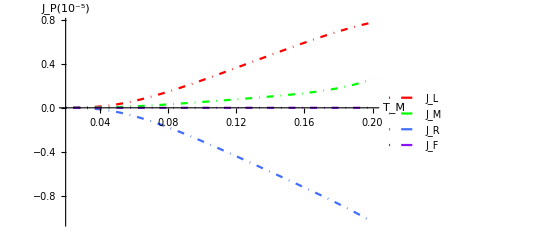

```mathematica
Module[{T1,T2min,T2max,κ1,κ2,κ3,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.20Tconv;T3=0.02Tconv;
κ1=0.01;κ2=0.01;κ3=0.01;
ωLs=0ωconv;ωMs=0ωconv;ωRs=0ωconv;
ωLMs=0.9ωconv;ωMRs=1.1ωconv;ωRLs=0ωconv;
Ωs=0.0ωconv;Tres=0.002Tconv;
PlotEngyFlowsWithTM[T1,T2min,T2max,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,Tres,True]
]
```

### Plots for adjusting Ω while keeping T_M constant (operation as an optically controlled thermal gate)

Inwards energy flows when temperature T_M is changed, keeping Ω constant,

```mathematica
PlotEngyFlowsWithΩ[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωmin_,Ωmax_,Ωres_,plotrange_]:=Module[{tempx,tempy,temp},
tempy=10^5 Table[Subscript[varEngyFunc, 1][T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
tempx=Table[{Ω,Ω,Ω,Ω},{Ω,Ωmin,Ωmax,Ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,4}];
ListPlot[temp,AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["Ω",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{Red,Green,BlueC,PurpleC},PlotLegends->{
Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_M",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_R",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},PlotRange->plotrange]
]
```

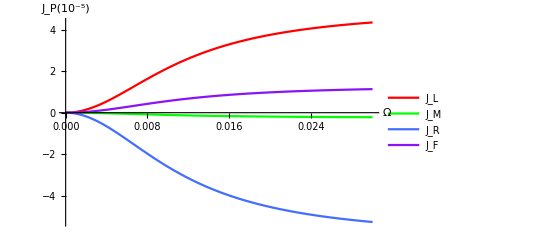

```mathematica
Module[{T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωmin,Ωmax,Ωres},
T1=0.2Tconv;T2=0.02Tconv;T3=0.02Tconv;
κ1=0.01;κ2=0.01;κ3=0.01;
ωLs=0ωconv;ωMs=0ωconv;ωRs=0ωconv;
ωLMs=0.9ωconv;ωMRs=1.1ωconv;ωRLs=0ωconv;
Ωmin=0ωconv;Ωmax=0.03ωconv;Ωres=0.0002ωconv;
PlotEngyFlowsWithΩ[T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωmin,Ωmax,Ωres,Full]
]
```

## Master equation of a optically controlled quantum thermal gate in a simplified 4×4 space

We make the following assumptions to simplify the previous 8-level system to a 4-level one,
	1. ω_L=ω_M=ω_R = 0
	2. ω_RL=0

```mathematica
MatrixForm[Simplify[Subscript[HsMatrix, S]/.{Subscript[ωL, S]->0,Subscript[ωM, S]->0,Subscript[ωR, S]->0,Subscript[ωRL, S]->0}]]
```

(1/2 ℏ (ωLM_S+ωMR_S) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 ℏ (ωLM_S-ωMR_S) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 ℏ (ωLM_S+ωMR_S) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 ℏ (-ωLM_S+ωMR_S) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_S-ωMR_S) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_S+ωMR_S) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_S-ωMR_S) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_S+ωMR_S))

### Reducing dimensionality of the density matrix under above energy assumptions

The previous 8 eigenstates group together in groups of 2,
|1> = |+z,+z,+z> = |-z,-z,-z>
|2> = |+z,+z,-z> = |-z,-z,+z>
|3> =|+z,-z,+z> = |-z,+z,-z> 
|4> =|+z,-z,-z> = |-z,+z,+z>

With these identities, the density matrix reduces to the following form

```mathematica
MapFunc[i_]:=(i,1+i,8)1+(i,2+i,7)2+(i,3+i,6)3+(i,4+i,5)4
ReduceDims[ρ_]:=Table[(1-a,b)∑_(i=1)^8 ∑_(j=1)^8 ρ[[i,j]]a,MapFunc[i]b,MapFunc[j] +  a,b∑_(i=1)^8 ρ[[i,i]]a,MapFunc[i],{a,1,4},{b,1,4}]
```

```mathematica
ReduceDims[Subscript[ρMatrix, S][t]]//MatrixForm
```

(ρ_(S,1,1)[t]+ρ_(S,8,8)[t] | ρ_(S,1,2)[t]+ρ_(S,1,7)[t]+ρ_(S,8,2)[t]+ρ_(S,8,7)[t] | ρ_(S,1,3)[t]+ρ_(S,1,6)[t]+ρ_(S,8,3)[t]+ρ_(S,8,6)[t] | ρ_(S,1,4)[t]+ρ_(S,1,5)[t]+ρ_(S,8,4)[t]+ρ_(S,8,5)[t]
ρ_(S,2,1)[t]+ρ_(S,2,8)[t]+ρ_(S,7,1)[t]+ρ_(S,7,8)[t] | ρ_(S,2,2)[t]+ρ_(S,7,7)[t] | ρ_(S,2,3)[t]+ρ_(S,2,6)[t]+ρ_(S,7,3)[t]+ρ_(S,7,6)[t] | ρ_(S,2,4)[t]+ρ_(S,2,5)[t]+ρ_(S,7,4)[t]+ρ_(S,7,5)[t]
ρ_(S,3,1)[t]+ρ_(S,3,8)[t]+ρ_(S,6,1)[t]+ρ_(S,6,8)[t] | ρ_(S,3,2)[t]+ρ_(S,3,7)[t]+ρ_(S,6,2)[t]+ρ_(S,6,7)[t] | ρ_(S,3,3)[t]+ρ_(S,6,6)[t] | ρ_(S,3,4)[t]+ρ_(S,3,5)[t]+ρ_(S,6,4)[t]+ρ_(S,6,5)[t]
ρ_(S,4,1)[t]+ρ_(S,4,8)[t]+ρ_(S,5,1)[t]+ρ_(S,5,8)[t] | ρ_(S,4,2)[t]+ρ_(S,4,7)[t]+ρ_(S,5,2)[t]+ρ_(S,5,7)[t] | ρ_(S,4,3)[t]+ρ_(S,4,6)[t]+ρ_(S,5,3)[t]+ρ_(S,5,6)[t] | ρ_(S,4,4)[t]+ρ_(S,5,5)[t])

Therefore we redefine a 4×4 density matrix,

```mathematica
Subscript[ρSimpMatrix, S_][t_]:=Table[Subscript[ρ, S,i,j][t],{i,1,4},{j,1,4}];
MatrixForm[Subscript[ρSimpMatrix, S][t]]
```

(ρ_(S,1,1)[t] | ρ_(S,1,2)[t] | ρ_(S,1,3)[t] | ρ_(S,1,4)[t]
ρ_(S,2,1)[t] | ρ_(S,2,2)[t] | ρ_(S,2,3)[t] | ρ_(S,2,4)[t]
ρ_(S,3,1)[t] | ρ_(S,3,2)[t] | ρ_(S,3,3)[t] | ρ_(S,3,4)[t]
ρ_(S,4,1)[t] | ρ_(S,4,2)[t] | ρ_(S,4,3)[t] | ρ_(S,4,4)[t])

### Reduced system Hamiltonian

Consider the previous system Hamiltonian, under the above assumptions

```mathematica
Subscript[HsMatrix, S]/.{Subscript[ωL, S_]->0,Subscript[ωM, S_]->0,Subscript[ωR, S_]->0,Subscript[ωRL, S_]->0}//Simplify//MatrixForm
```

(1/2 ℏ (ωLM_S+ωMR_S) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 ℏ (ωLM_S-ωMR_S) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 ℏ (ωLM_S+ωMR_S) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 ℏ (-ωLM_S+ωMR_S) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_S-ωMR_S) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_S+ωMR_S) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_S-ωMR_S) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_S+ωMR_S))

Observing the degeneracies, construct the 4×4 system Hamiltonian

```mathematica
Subscript[HsSimpMatrix, S_]:=({{1/2 ℏ (Subscript[ωLM, S]+Subscript[ωMR, S]), 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωLM, S]-Subscript[ωMR, S]), 0, 0}, {0, 0, -1/2 ℏ (Subscript[ωLM, S]+Subscript[ωMR, S]), 0}, {0, 0, 0, 1/2 ℏ (-Subscript[ωLM, S]+Subscript[ωMR, S])}})
```

### Transforming field interactions

Consider the previous field interaction Hamiltonian,

```mathematica
Subscript[HlMatrix, S]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ℏ Ω_S)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ℏ Ω_S)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_S)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ℏ Ω_S)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The 4×4 version can now be written as

```mathematica
Subscript[HlSimpMatrix, S_]:=({{0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, S])/2}, {0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, S])/2, 0, 0}})
```

We can understand the above form since  the field should now be driving the |2> →|4> and |4> →|2> transitions. The interaction strength Ω_S is artificially halved because two transitions are consolidated into one.

### Transforming dissipative terms

Consider the previous Lindblad operators

```mathematica
Table[MatrixForm[Subscript[AMatrix, P][i]],{P,1,3},{i,1,4}]//MatrixForm
Table[MatrixForm[Subscript[ω, P][i]],{P,1,3},{i,1,4}]//MatrixForm
```

((0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))

(ω_(5,1) | ω_(6,2) | ω_(7,3) | ω_(8,4)
ω_(3,1) | ω_(4,2) | ω_(7,5) | ω_(8,6)
ω_(2,1) | ω_(4,3) | ω_(6,5) | ω_(8,7))

Reducing their dimensionality give us the following operators, and frequencies.

```mathematica
Table[MatrixForm[ReduceDims[Subscript[AMatrix, P][i]]],{P,1,3},{i,1,4}]//MatrixForm
Table[MatrixForm[Subscript[ω, P][i]],{P,1,3},{i,1,4}]/.Subscript[ω, i_,j_]->Subscript[ω, MapFunc[i],MapFunc[j]]//MatrixForm
```

((0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)
(0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0) | (0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

(ω_(4,1) | ω_(3,2) | ω_(2,3) | ω_(1,4)
ω_(3,1) | ω_(4,2) | ω_(2,4) | ω_(1,3)
ω_(2,1) | ω_(4,3) | ω_(3,4) | ω_(1,2))

We note that only two out of the four can correspond to positive transitions,

```mathematica
Subscript[ASimpMatrix, P_][i_]:=Table[ReduceDims[Subscript[AMatrix, Ps][is]],{Ps,1,3},{is,1,2}][[P,i]]
Subscript[ωSimp, P_][i_]:=(Table[Subscript[ω, Ps][is],{Ps,1,3},{is,1,2}]/.Subscript[ω, a_,b_]->Subscript[ω, MapFunc[a],MapFunc[b]])[[P,i]]
```

```mathematica
Table[Subscript[ASimpMatrix, P][i],{P,1,3},{i,1,2}]//MatrixForm
Table[Subscript[ωSimp, P][i],{P,1,3},{i,1,2}]//MatrixForm
```

((0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0))

(ω_(4,1) | ω_(3,2)
ω_(3,1) | ω_(4,2)
ω_(2,1) | ω_(4,3))

Insert a “transistor number” variable S,

```mathematica
Subscript[ASimpMatrix, S_,P_][i_]:=Subscript[ASimpMatrix, P][i]
Subscript[ωSimp, S_,P_][i_]:=Subscript[ωSimp, P][i]/.Subscript[ω, j_,k_]->Subscript[ω, S,j,k]
```

The dissipation terms can now be written

```mathematica
Subscript[LinSimpMatrix, S_,P_][ρ_]:=Subscript[LinSimpMatrix, S,P][ρ]=∑_(i=1)^2 (Subscript[J, S,P][Subscript[ωSimp, S,P][i]](1+Subscript[NBE, S,P][Subscript[ωSimp, S,P][i]])(Subscript[ASimpMatrix, S,P][i].ρ.Subscript[ASimpMatrix, S,P][i]†-1/2(Subscript[ASimpMatrix, S,P][i]†.Subscript[ASimpMatrix, S,P][i].ρ+ρ.Subscript[ASimpMatrix, S,P][i]†.Subscript[ASimpMatrix, S,P][i]))+Subscript[J, S,P][Subscript[ωSimp, S,P][i]]Subscript[NBE, S,P][Subscript[ωSimp, S,P][i]](Subscript[ASimpMatrix, S,P][i]†.ρ.Subscript[ASimpMatrix, S,P][i]-1/2(Subscript[ASimpMatrix, S,P][i].Subscript[ASimpMatrix, S,P][i]†.ρ+ρ.Subscript[ASimpMatrix, S,P][i].Subscript[ASimpMatrix, S,P][i]†)))
```

```mathematica
ReplaceArithmetically[Subscript[LinSimpMatrix, S,1][Subscript[ρSimpMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinSimpMatrix, S,2][Subscript[ρSimpMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinSimpMatrix, S,3][Subscript[ρSimpMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]]
];
MatrixForm[%]
```

(Τ_(S,1)[4,1] | 1/2 (-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,1,2)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,1,3)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,1,3)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,1)[ω_(S,4,1)] ρ_(S,1,4)[t]-2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,4)[t])
1/2 (-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,1)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,2,1)[t]) | Τ_(S,1)[3,2] | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,2,3)[t]-2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,1)[ω_(S,4,1)] ρ_(S,2,4)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,4)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,2,4)[t])
1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,3,1)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,3,1)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,3,2)[t]-2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,3,2)[t]) | -Τ_(S,1)[3,2] | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,3,4)[t]-J_(S,1)[ω_(S,4,1)] ρ_(S,3,4)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,3,4)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,3,4)[t])
1/2 (-J_(S,1)[ω_(S,4,1)] ρ_(S,4,1)[t]-2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,1)[ω_(S,4,1)] ρ_(S,4,2)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,4,2)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,4,3)[t]-J_(S,1)[ω_(S,4,1)] ρ_(S,4,3)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,4,3)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,4,3)[t]) | -Τ_(S,1)[4,1])

(Τ_(S,2)[3,1] | 1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]-2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,1,4)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,4)[t])
1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,1)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,1)[t]) | Τ_(S,2)[4,2] | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,2,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,3)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t]-2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t])
1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]-2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,2)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,2)[t]) | -Τ_(S,2)[3,1] | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,4,2)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,4)[t])
1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,1)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,1)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]-2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,4,2)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,3)[t]) | -Τ_(S,2)[4,2])

(Τ_(S,3)[2,1] | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]-2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,1,4)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,4)[t])
1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]-2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]) | -Τ_(S,3)[2,1] | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,3)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,4,3)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,4)[t])
1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,1)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,3,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,2)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,2)[t]) | Τ_(S,3)[4,3] | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t]-2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t])
1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,1)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,1)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,4,3)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]-2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]) | -Τ_(S,3)[4,3])

### Quantum Markovian master equation

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
Subscript[RHSfieldSimp, S_]:=-ⅈ/ℏ(Subscript[HlSimpMatrix, S].Subscript[ρSimpMatrix, S][t]-Subscript[ρSimpMatrix, S][t].Subscript[HlSimpMatrix, S]);

Subscript[RHSSimp, S_]:=Subscript[RHSfieldSimp, S]+Subscript[LinSimpMatrix, S,1][Subscript[ρSimpMatrix, S][t]]+Subscript[LinSimpMatrix, S,2][Subscript[ρSimpMatrix, S][t]]+Subscript[LinSimpMatrix, S,3][Subscript[ρSimpMatrix, S][t]];

MatrixForm[Subscript[RHSSimp, S]]
```

(-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,1)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,1)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,1)[t]+J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,2)[t]+J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,3)[t]+J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,4)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,1,2)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,2)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,1,2)[t]-1/2 ⅈ Ω_S ρ_(S,1,4)[t] | -1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,1,3)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,1,3)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,3)[t] | -1/2 ⅈ Ω_S ρ_(S,1,2)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,4)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,1,4)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,1,4)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,1,4)[t]
-1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,1)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,2,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,1)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,1)[t]+1/2 ⅈ Ω_S ρ_(S,4,1)[t] | J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,1)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,2)[t]-J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,2)[t]+J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,3)[t]-(ⅈ (1/2 ℏ Ω_S ρ_(S,2,4)[t]-1/2 ℏ Ω_S ρ_(S,4,2)[t]))/ℏ+J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,4)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,3)[t]-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,2,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,2,3)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,3)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,3)[t]+1/2 ⅈ Ω_S ρ_(S,4,3)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,4)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,2,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,2,4)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,2,4)[t]-(ⅈ (1/2 ℏ Ω_S ρ_(S,2,2)[t]-1/2 ℏ Ω_S ρ_(S,4,4)[t]))/ℏ
-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,1)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,3,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,1)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,1)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,3,2)[t]-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,2)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,3,2)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,2)[t]-1/2 ⅈ Ω_S ρ_(S,3,4)[t] | J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,1)[t]+J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,2)[t]-J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,3)[t]-J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,3)[t]+J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,4)[t] | -1/2 ⅈ Ω_S ρ_(S,3,2)[t]-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,4)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,3,4)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,3,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,3,4)[t]
1/2 ⅈ Ω_S ρ_(S,2,1)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,4,1)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,1)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,1)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,1)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,4,2)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,4,2)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,2)[t]-(ⅈ (-1/2 ℏ Ω_S ρ_(S,2,2)[t]+1/2 ℏ Ω_S ρ_(S,4,4)[t]))/ℏ | 1/2 ⅈ Ω_S ρ_(S,2,3)[t]-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,4,3)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,4,3)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,3)[t] | J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,1)[t]+J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,2)[t]+J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,3)[t]-(ⅈ (-1/2 ℏ Ω_S ρ_(S,2,4)[t]+1/2 ℏ Ω_S ρ_(S,4,2)[t]))/ℏ-J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,4)[t]-J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,4)[t]-J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,4)[t])

```mathematica
Subscript[LHSSimp, S_]:=D[Subscript[ρSimpMatrix, S][t], t];

MatrixForm[Subscript[LHSSimp, S]]
```

(ρ_(S,1,1)'[t] | ρ_(S,1,2)'[t] | ρ_(S,1,3)'[t] | ρ_(S,1,4)'[t]
ρ_(S,2,1)'[t] | ρ_(S,2,2)'[t] | ρ_(S,2,3)'[t] | ρ_(S,2,4)'[t]
ρ_(S,3,1)'[t] | ρ_(S,3,2)'[t] | ρ_(S,3,3)'[t] | ρ_(S,3,4)'[t]
ρ_(S,4,1)'[t] | ρ_(S,4,2)'[t] | ρ_(S,4,3)'[t] | ρ_(S,4,4)'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
Subscript[motioneqSimp, S_]:=Flatten[Solve[Subscript[LHSSimp, S]==Subscript[RHSSimp, S],Flatten[Table[Subscript[ρ, S,i,j]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal]
```

Separate diagonal and off diagonal equations,

```mathematica
Subscript[motioneqdiagSimp, S_]:=Subscript[motioneqSimp, S][[1;; ;;5]];
Subscript[motioneqoffdiagSimp, S_]:=Delete[Subscript[motioneqSimp, S],Table[{1+5i},{i,0,3}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
Subscript[motioneqdiagtranSimp, S_]:=
ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
]&,Subscript[motioneqdiagSimp, S]]
```

### Equations of motion for the individual transistors

Actual equations for population densities (i.e. diagonal elements of the density matrix),

```mathematica
Subscript[motioneqdiagSimp, S];
```

Simplified version of the same equations,

```mathematica
Subscript[motioneqdiagtranSimp, S]
```

{ρ_(S,1,1)'[t]==Τ_(S,1)[4,1]+Τ_(S,2)[3,1]+Τ_(S,3)[2,1],ρ_(S,2,2)'[t]==-Υ_S[2,4]+Τ_(S,1)[3,2]+Τ_(S,2)[4,2]-Τ_(S,3)[2,1],ρ_(S,3,3)'[t]==-Τ_(S,1)[3,2]-Τ_(S,2)[3,1]+Τ_(S,3)[4,3],ρ_(S,4,4)'[t]==Υ_S[2,4]-Τ_(S,1)[4,1]-Τ_(S,2)[4,2]-Τ_(S,3)[4,3]}

### Dynamical heat flows

Calculate heat current inflow, from the thermal bath into the transistor

```mathematica
Subscript[HsSimpMatrixSimp, S_]:=DiagonalMatrix[ℏ{Subscript[ω, S,1],Subscript[ω, S,2],Subscript[ω, S,3],Subscript[ω, S,4]}];
```

```mathematica
Subscript[EngyFlowInSimp, S_,P_]:=Tr[Subscript[LinSimpMatrix, S,P][Subscript[ρSimpMatrix, S][t]].Subscript[HsSimpMatrixSimp, S]]
Subscript[EngyFlowInFieldSimp, S_]:=Tr[Subscript[RHSfieldSimp, S].Subscript[HsSimpMatrix, S]]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowInSimp, S,1],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
]

ReplaceArithmetically[Subscript[EngyFlowInSimp, S,2],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
]

ReplaceArithmetically[Subscript[EngyFlowInSimp, S,3],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
]

ReplaceArithmetically[Subscript[EngyFlowInFieldSimp, S],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
];
Simplify[%]
```

(ℏ ω_(S,2)-ℏ ω_(S,3)) Τ_(S,1)[3,2]+(ℏ ω_(S,1)-ℏ ω_(S,4)) Τ_(S,1)[4,1]

(ℏ ω_(S,1)-ℏ ω_(S,3)) Τ_(S,2)[3,1]+(ℏ ω_(S,2)-ℏ ω_(S,4)) Τ_(S,2)[4,2]

(ℏ ω_(S,1)-ℏ ω_(S,2)) Τ_(S,3)[2,1]+(ℏ ω_(S,3)-ℏ ω_(S,4)) Τ_(S,3)[4,3]

-ℏ (ωLM_S-ωMR_S) Υ_S[2,4]

### On unit conversions

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

### Density matrix, transition rate and energy flow at equilibrium

Function for density matrix elements, transition rates and energy flows,

```mathematica
Subscript[varFuncSimp, S_][T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLMs_,ωMRs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum,NBEassum,unitassum,Subscript[κ, S,1]-> κ1,Subscript[κ, S,2]-> κ2,Subscript[κ, S,3]-> κ3,Subscript[Ω, S]->Ωs,Subscript[T, S,1]-> T1,Subscript[T, S,2]-> T2,Subscript[T, S,3]-> T3,Subscript[ωL, S]->0,Subscript[ωM, S]->0,Subscript[ωR, S]->0,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->0}];
temp1=N[Subscript[motioneqSimp, S]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, S,i_,j_]'[t]-> 0,Subscript[ρ, S,i_,j_][t]-> Subscript[ρ, S,i,j]},1==∑_(i=1)^4 Subscript[ρ, S,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, S,i,j],{i,1,4},{j,1,4}]]]]];
Re[{Flatten[
Table[Subscript[ρ, S,i,i],{i,1,4}]/.temp3],
Flatten[{
Subscript[Τs, S,1][4,1],Subscript[Τs, S,1][3,2],
Subscript[Τs, S,2][3,1],Subscript[Τs, S,2][4,2],
Subscript[Τs, S,3][2,1],Subscript[Τs, S,3][4,3],
Subscript[Υs, S][4,2]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],temp0}]/.temp3],
Flatten[{
Subscript[EngyFlowInSimp, S,1],Subscript[EngyFlowInSimp, S,2],Subscript[EngyFlowInSimp, S,3],Subscript[EngyFlowInFieldSimp, S]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],ωassum1,temp0}]/.temp3]}]
]
```

```mathematica
Subscript[varFuncSimp, 1][0.2,0.06,0.02,0.01,0.01,0.01,1.1,0.9,0.01,unitassum]//.ωassum
```

{{1.58863×10^-6,0.0029178,0.995671,0.00140936},{4.60704×10^-8,0.000012716,-3.17727×10^-8,-5.94721×10^-6,-1.42977×10^-8,0.0000126842,-6.7831×10^-6},{0.0000140383,-1.25299×10^-6,-0.0000114287,-1.35662×10^-6}}

Function for drawing a state flow diagram,

```mathematica
DrawFuncSimp[S_,ωLMs_,ωMRs_,title_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,temp0},
temp0=Flatten[{Jassum,NBEassum,k->1,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs}];label={"|1_SIMP>=|↑↑↑> |↓↓↓>","|2_SIMP>=|↑↑↓> |↓↓↑>","|3_SIMP>=|↑↓↑> |↓↑↓>","|4_SIMP>=|↑↓↓> |↓↑↑>"};posx={0,-0.5,0,0.5};posy=Diagonal[Subscript[HsSimpMatrix, S]/(ℏ ωconv)/.Flatten[{Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs}]];nodes=var[[1]];rates=({{0, -var[[2]][[5]], -var[[2]][[3]], -var[[2]][[1]]}, {0, 0, -var[[2]][[2]], -var[[2]][[4]]}, {0, 0, 0, -var[[2]][[6]]}, {0, 0, 0, 0}});
ratesF=({{0, 0, 0, 0}, {0, 0, 0, -var[[2]][[7]]}, {0, 0, 0, 0}, {0, 0, 0, 0}});ratecolors=({{0, BlueC, Green, Red}, {0, 0, Red, Green}, {0, 0, 0, BlueC}, {0, 0, 0, 0}});
ratecolorsF=({{0, 0, 0, 0}, {0, 0, 0, PurpleC}, {0, 0, 0, 0}, {0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues, plotted for dynamically changeable bath, field and system parameters,

```mathematica
Manipulate[Module[{temp},
temp=Subscript[varFuncSimp, 1][T1,T2,T3,κ1,κ2,κ3,ωLMs,ωMRs,Ωs,unitassum];
{
DrawFuncSimp[1,ωLMs,ωMRs,StringForm["Transistor 4x4"],Τmax,temp],

BarChart[temp[[3]]
,ChartLabels->{"Left ","Mid","Right","Field"},PlotLabel->"Equilibrium energy inflow",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax,Emax},ChartStyle->{Red,Green,BlueC,PurpleC}],

BarChart[temp[[2]]
,ChartLabels->Placed[{"L |4> to |1>","L |3> to |2>","M |3> to |1>","M |4> to |2>","R |2> to |1>","R |4> to |3>","F |4> to |2>"},Center,Rotate[#,π/2]&],PlotLabel->"Equilibrium thermal transition rate",ImageSize->Medium,ChartStyle->{Red,Red,Green,Green,BlueC,BlueC,PurpleC}],

BarChart[temp[[1]]
,ChartLabels->{"ρ_{1, 1}","ρ_{2, 2}","ρ_{3, 3}","ρ_{4, 4}","ρ_{5, 5}","ρ_{6, 6}","ρ_{7, 7}","ρ_{8, 8}"},PlotLabel->"Equilibrium density matrix",ImageSize->Medium,PlotRange->{-0.1,1},ChartStyle->"Pastel"]
}],
Delimiter,Item["Bath Temperatures",Alignment->Center],
{{T1,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{T2,0.1 Tconv},0.01 Tconv,0.22 Tconv},
{{T3,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κ1,0.01},0.001,0.2},
{{κ2,0.01},0.001,0.2},
{{κ3,0.01},0.001,0.2},
Delimiter,Item["System Parameters",Alignment->Center],
{{ωLMs,0.9ωconv},0ωconv,2ωconv},
{{ωMRs,1.1ωconv},0ωconv,2ωconv},
Delimiter,Item["Optical Field Intensity",Alignment->Center],
{{Ωs,0.005ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Τmax,0.00006Τconv},0.000001Τconv,0.0002Τconv}]
```

Function for more quickly calculating the inwards energy flows,

```mathematica
Subscript[varEngyFuncSimp, S_][T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLMs_,ωMRs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum,NBEassum,unitassum,Subscript[κ, S,1]-> κ1,Subscript[κ, S,2]-> κ2,Subscript[κ, S,3]-> κ3,Subscript[Ω, S]->Ωs,Subscript[T, S,1]-> T1,Subscript[T, S,2]-> T2,Subscript[T, S,3]-> T3,Subscript[ωL, S]->0,Subscript[ωM, S]->0,Subscript[ωR, S]->0,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->0}];
temp1=N[Subscript[motioneqSimp, S]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, S,i_,j_]'[t]-> 0,Subscript[ρ, S,i_,j_][t]-> Subscript[ρ, S,i,j]},1==∑_(i=1)^4 Subscript[ρ, S,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, S,i,j],{i,1,4},{j,1,4}]]]]];
Re[Flatten[{
Subscript[EngyFlowInSimp, S,1],Subscript[EngyFlowInSimp, S,2],Subscript[EngyFlowInSimp, S,3],Subscript[EngyFlowInFieldSimp, S]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],ωassum1,temp0}]/.temp3]]
]
```

```mathematica
Subscript[varEngyFuncSimp, 1][0.2,0.02,0.02,0.01,0.01,0.01,1.1,0.9,0.02,unitassum]
```

{0.0000187053,-1.09857×10^-6,-0.0000152282,-2.37861×10^-6}

### Plots for adjusting T_M while keeping Ω constant (operation as a thermal transistor)

Inwards energy flows when temperature T_M is changed, keeping Ω constant,

```mathematica
PlotEngyFlowsWithTMSimp[T1_,T2min_,T2max_,T3_,κ1_,κ2_,κ3_,ωLMs_,ωMRs_,Ωs_,Tres_,legends_]:=Module[{tempx,tempy,temp},
tempx=Table[{T2,T2,T2,T2},{T2,T2min,T2max,Tres}];
tempy=10^5 Table[Subscript[varEngyFuncSimp, 1][T1,T2,T3,κ1,κ2,κ3,ωLMs,ωMRs,Ωs,unitassum],{T2,T2min,T2max,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,4}];
ListPlot[temp,PlotRange->{{T2min,T2max},Full},AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["T_M",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{{Red,DotDashed},{Green,DotDashed},{BlueC,DotDashed},{PurpleC,DotDashed}},PlotLegends->legends &&{
Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_M",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_R",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

```mathematica
Module[{T1,T2min,T2max,κ1,κ2,κ3,T3,ωLMs,ωMRs,Ωs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.20Tconv;T3=0.02Tconv;
κ1=0.01;κ2=0.01;κ3=0.01;
ωLMs=0.9ωconv;ωMRs=1.1ωconv;
Ωs=0.0ωconv;Tres=0.002Tconv;
PlotEngyFlowsWithTMSimp[T1,T2min,T2max,T3,κ1,κ2,κ3,ωLMs,ωMRs,Ωs,Tres,True]
]

Module[{T1,T2min,T2max,κ1,κ2,κ3,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.20Tconv;T3=0.02Tconv;
κ1=0.01;κ2=0.01;κ3=0.01;
ωLs=0ωconv;ωMs=0ωconv;ωRs=0ωconv;
ωLMs=0.9ωconv;ωMRs=1.1ωconv;ωRLs=0ωconv;
Ωs=0.0ωconv;Tres=0.002Tconv;
PlotEngyFlowsWithTM[T1,T2min,T2max,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,Tres,True]
]
```

-Graphics-

-Graphics-

### Plots for adjusting Ω while keeping T_M constant (operation as an optically controlled thermal gate)

Inwards energy flows when temperature T_M is changed, keeping Ω constant,

```mathematica
PlotEngyFlowsWithΩSimp[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLMs_,ωMRs_,Ωmin_,Ωmax_,Ωres_,plotrange_]:=Module[{tempx,tempy,temp},
tempy=10^5 Table[Subscript[varEngyFuncSimp, 1][T1,T2,T3,κ1,κ2,κ3,ωLMs,ωMRs,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
tempx=Table[{Ω,Ω,Ω,Ω},{Ω,Ωmin,Ωmax,Ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,4}];
ListPlot[temp,AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],AxesLabel->{
Style["Ω",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},Joined->True,PlotStyle->{Red,Green,BlueC,PurpleC},PlotLegends->{
Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_M",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_R",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},PlotRange->plotrange]
]
```

```mathematica
Module[{T1,T2,T3,κ1,κ2,κ3,ωLMs,ωMRs,Ωmin,Ωmax,Ωres},
T1=0.2Tconv;T2=0.02Tconv;T3=0.02Tconv;
κ1=0.01;κ2=0.01;κ3=0.01;
ωLMs=0.9ωconv;ωMRs=1.1ωconv;
Ωmin=0ωconv;Ωmax=0.03ωconv;Ωres=0.0002ωconv;
PlotEngyFlowsWithΩSimp[T1,T2,T3,κ1,κ2,κ3,ωLMs,ωMRs,Ωmin,Ωmax,Ωres,Full]
]

Module[{T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωmin,Ωmax,Ωres},
T1=0.2Tconv;T2=0.02Tconv;T3=0.02Tconv;
κ1=0.01;κ2=0.01;κ3=0.01;
ωLs=0ωconv;ωMs=0ωconv;ωRs=0ωconv;
ωLMs=0.9ωconv;ωMRs=1.1ωconv;ωRLs=0ωconv;
Ωmin=0ωconv;Ωmax=0.03ωconv;Ωres=0.0002ωconv;
PlotEngyFlowsWithΩ[T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωmin,Ωmax,Ωres,Full]
]
```

-Graphics-

-Graphics-